```mathematica
Needs["ErrorBarPlots`"]
```

```mathematica
PBrody[x_,w_]:=(1+w)(Gamma[(2+w)/(1+w)])^(1+w)x^w Exp[-(Gamma[(2+w)/(1+w)]x)^(1+w)];
```

```mathematica
BrodyDistribution=ProbabilityDistribution[PBrody[x,w],{x,0,∞},Assumptions->w>0]
```

ProbabilityDistribution[x^w ⅇ^(-(x Gamma[(2+w)/(1+w)])^(1+w)) (1+w) Gamma[(2+w)/(1+w)]^(1+w),{x,0,∞},Assumptions→w>0]

```mathematica
FitError[func_,list_,p_]:=Module[{tab1,nbin},
tab1=Table[(list[[i,2]]-func[list[[i,1]],p])^2,{i,1,Length[list]}];
If[p==Null,
tab1=Table[(list[[i,2]]-func[list[[i,1]]])^2,{i,1,Length[list]}],
tab1=Table[(list[[i,2]]-func[list[[i,1]],p])^2,{i,1,Length[list]}]
];
nbin=Length[tab1];
√(Total[tab1]/(nbin-1))
]
```

```mathematica
ResidualSum[func_,P_,param_]:=Module[{tab1,nbin,Ntot,dbin},
Ntot=Total[P[[All,2]]];
dbin=P[[2,1]]-P[[1,1]];
tab1=Table[(P[[i,2]]- func[P[[i,1]],param])^2,{i,1,Length[P]}];
Total[tab1]
]
```

```mathematica
ChiSqr[func_,hist_,p_]:=Module[{tab1,nbin,dbin,Ntot},
dbin=hist[[2,1]]-hist[[1,1]];
Ntot=Total[hist[[All,2]]];
tab1=Table[(hist[[i,2]]-Ntot  dbin func[hist[[i,1]],p])^2/(Ntot dbin  func[hist[[i,1]],p]),{i,1,Length[hist]}];
If[p== Null,
tab1=Table[(hist[[i,2]]-Ntot  dbin func[hist[[i,1]]])^2/(Ntot dbin  func[hist[[i,1]]]),{i,1,Length[hist]}]
];
nbin=Length[hist];
Total[tab1]
]
RedChiSqr[func_,hist_,p_,numfit_]:=ChiSqr[func,hist,p]/(Length[hist]-numfit);
```

```mathematica
SemiPoisson[s_]:=4 s Exp[-2 s]
```

```mathematica
SemiPoissonDistribution=ProbabilityDistribution[SemiPoisson[x],{x,0,∞}]
```

ProbabilityDistribution[4 x ⅇ^(-2 x),{x,0,∞}]

```mathematica
iens=1;icoup=2;
```

```mathematica
path1=StringJoin[{"~/Code/Nchannel/Square/CODES/resdata_from_morgoth/end-cases/fort.",ToString[iens*1000+icoup]}]
(*path1=StringJoin[{"~/Code/Nchannel/Square/CODES/fort.",ToString[iens*1000+icoup]}]*)
```

~/Code/Nchannel/Square/CODES/resdata_from_morgoth/end-cases/fort.1002

```mathematica
Data=DeleteCases[Import[path1,"Table"],{}];
```

```mathematica
iemax=Length[Data];iemin=1;
sigma=Table[{Data[[ie,2]],Data[[ie,10]]},{ie,iemin,iemax}];
lzclose=Table[{Data[[ie,2]], Log[Data[[ie,6]]]},{ie,iemin,iemax}];
alsqr=Table[{Data[[ie,2]],Data[[ie,5]]},{ie,iemin,iemax}];
albgsqr=Table[{Data[[ie,2]],Sin[Data[[ie,8]]]^2},{ie,iemin,iemax}];
phaseopi=Table[{Data[[ie,2]],Data[[ie,11]]},{ie,iemin,iemax}];
ltimedelay=Table[{Data[[ie,2]],Log[Data[[ie,12]]]},{ie,iemin,iemax}];
ascat = Table[{Data[[ie,2]],Data[[ie,4]]},{ie,iemin,iemax}];
abg=  Table[{Data[[ie,2]],Data[[ie,13]]},{ie,iemin,iemax}];
BSdet = Table[{Data[[ie,2]],Data[[ie,7]]},{ie,iemin,iemax}];
```

```mathematica
padding={{100,45},{80,0}};
imgsize={600,300};
yrange=All;
xrange={0,0.1};
aspctratio=Full;1/GoldenRatio;
pabg=ListPlot[abg,Joined->True,PlotStyle->Black,Frame->True,FrameLabel->{"E/(ℏ^2/2μr_0^2)","a_bg/r_0"},LabelStyle->{16},PlotRange->{xrange,{-1000,1000}},GridLines->Automatic,ImageSize->imgsize,ImagePadding->padding,AspectRatio->aspctratio];
palsqr=ListPlot[{alsqr,albgsqr},Joined->True,PlotStyle->{{Black},{Red,Dotted}},Frame->True,FrameLabel->{"E/(ℏ^2/2μ r_0^2)",TraditionalForm[Sin[δ]^2]},LabelStyle->{16},PlotRange->{xrange,yrange},GridLines->Automatic,ImageSize->imgsize,ImagePadding->padding,AspectRatio->aspctratio,FrameTicks->{Automatic,Automatic}];
psigma=ListPlot[sigma,Joined->True,PlotStyle->Black,Frame->True,FrameLabel->{"E/(ℏ^2/2μr_0^2)","σ/r_0^2"},LabelStyle->{16},PlotRange->{xrange,yrange},GridLines->Automatic,ImageSize->imgsize,ImagePadding->padding,AspectRatio->aspctratio];
pstair=ListPlot[phaseopi,Joined->True,PlotStyle->Black,Frame->True,FrameLabel->{"E/(ℏ^2/2μr_0^2)","δ_0/π"},LabelStyle->{16},PlotRange->{xrange,All},GridLines->Automatic,ImageSize->imgsize,ImagePadding->padding,AspectRatio->aspctratio];
plzc=ListPlot[lzclose,Joined->True,PlotStyle->{Red,Dashed},Frame->True,FrameLabel->{"E/(ℏ^2/2μr_0^2)","log(Z_C)"},LabelStyle->{16},PlotRange->{xrange,{-7,18}},GridLines->Automatic,ImageSize->{600,250},ImagePadding->{{100,45},{8,8}},AspectRatio->aspctratio,ImageMargins->0,FrameTicksStyle->{{Automatic,Automatic},{Directive[FontOpacity->0,FontSize->0],Automatic}}];
pltd=ListPlot[ltimedelay,Joined->True,PlotStyle->Black,Frame->True,FrameLabel->{(*"E/(ℏ^2/2μr_0^2)"*)None,TraditionalForm[Log[(τ ℏ)/(2μ Subscript[r, 0]^2)]]},LabelStyle->Large,PlotRange->{xrange,{-7,18}},GridLines->Automatic,FrameTicks->{Automatic,Automatic},ImageSize->{600,250},ImagePadding->{{100,45},{8,8}},AspectRatio->aspctratio,ImageMargins->0,FrameTicksStyle->{{Automatic,Automatic},{Directive[FontOpacity->0,FontSize->0],Automatic}}];
pascat=ListPlot[ascat,Joined->True,PlotStyle->Black,Frame->True,FrameLabel->{"E/(ℏ^2/2μr_0^2)","a/r_0"},LabelStyle->{16},PlotRange->{xrange,{-100,100}},GridLines->Automatic,ImageSize->imgsize,ImagePadding->padding,AspectRatio->aspctratio];
```

```mathematica
pbsdet=ListPlot[BSdet,Joined->True,PlotStyle->Black,Frame->True,LabelStyle->{16},PlotRange->{xrange,{-10^-100,10^-100}},AspectRatio->50/1000,ImageSize->{600,50},PlotRangeClipping->False,ImagePadding->{{100,45},{0,20}},FrameTicks->{None,None},ImageMargins->0,Axes->False,Epilog->{Text[Style["(d)",Bold,22],{-0.015,0}]}]
```

-Graphics-

```mathematica
AllResData=DeleteCases[Import["~/Code/Nchannel/Square/CODES/resdata_from_morgoth/end-cases/fort.800","Table"],{}];
(*AllResData=DeleteCases[Import["~/Code/Nchannel/Square/CODES/fort.800","Table"],{}];*)
ResData[iens_,icoup_]:=Select[Select[AllResData,(#[[2]]==iens)&],(#[[3]]==icoup)&]
Resonances = ResData[iens,icoup];
NumRes=Length[Resonances];

ResLines=Table[ssbg  (EE-ER+q Γ/2)^2/((EE-ER)^2+(Γ/2)^2)/.{ssbg->Resonances[[ires,9]],ER->Resonances[[ires,5]],Γ->Resonances[[ires,7]],q->Resonances[[ires,8]]},{ires,1,NumRes}];
resplots=Table[Plot[Evaluate[ResLines[[ires]]],{EE,Resonances[[ires,5]]-2Resonances[[ires,7]],Resonances[[ires,5]]+2Resonances[[ires,7]]},PlotStyle->{Blue,Dashed},PlotRange->All,ImagePadding->padding,ImageSize->imgsize,AspectRatio->Full],{ires,1,NumRes}];
```

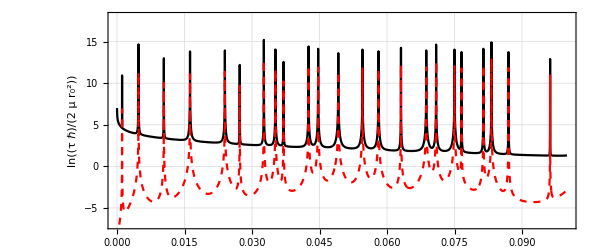

```mathematica
ptdlz=Show[{pltd,plzc},PlotRange->{xrange,{-7,18}},FrameLabel->{{TraditionalForm[ln[(τ ℏ)/(2μ Subscript[r, 0]^2)] ],Style["ln(Z_C/r_0)",Red]},{None,None}},PlotRangeClipping->False,Epilog->{Text[Style["(e)",Bold,22],{-.015,15.}]}]
```

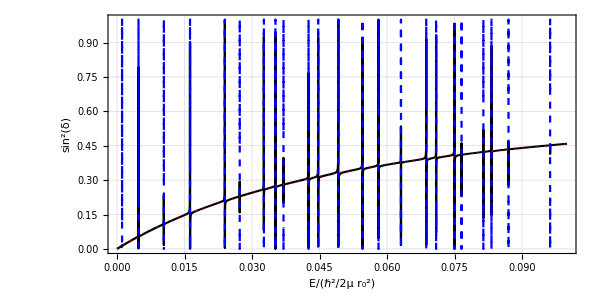

```mathematica
pfanolines = Show[{palsqr,resplots},PlotRange->{xrange,{0,1}},LabelStyle->Large,PlotRangeClipping->False,Epilog->{Text[Style["(f)",Bold,22],{-.015,0.9}]}]
```

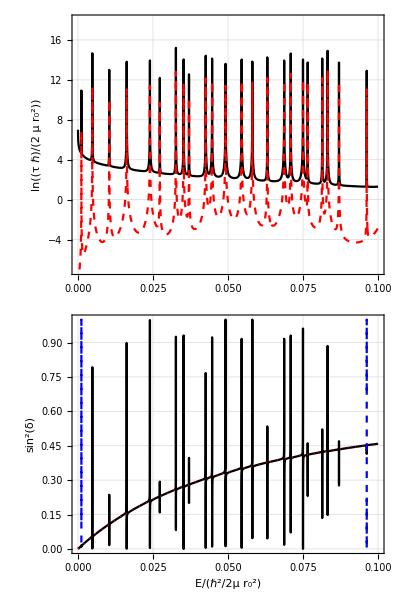

```mathematica
p1=Grid[{{pbsdet},{ptdlz},{pfanolines}},Spacings->0]
```

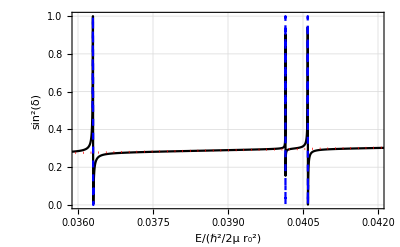

```mathematica
pfanofits=Show[pfanolines,PlotRange->{{0.036,0.042},All},ImagePadding->Automatic,ImageSize->Automatic,AspectRatio->1/GoldenRatio,PlotRangeClipping->True]
```

```mathematica
Export["~/Code/Nchannel/Square/CODES/plots/p-fanofits.pdf",pfanofits]
```

~/Code/Nchannel/Square/CODES/plots/p-fanofits.pdf

```mathematica
Export["~/Code/Nchannel/Square/CODES/plots/p-poisson-scat.pdf",p1]
```

~/Code/Nchannel/Square/CODES/plots/p-poisson-scat.pdf

```mathematica
Export["~/Code/Nchannel/Square/CODES/plots/p-wigner-scat.pdf",p1]
```

~/Code/Nchannel/Square/CODES/plots/p-wigner-scat.pdf

```mathematica
Export["~/Code/Nchannel/Square/CODES/plots/p-tridiag-chris-3chan-scat.pdf",p1]
```

~/Code/Nchannel/Square/CODES/plots/p-tridiag-chris-3chan-scat.pdf

### Statistical Data

```mathematica
AllResonanceData=Import["~/Code/Nchannel/Square/CODES/resdata_from_morgoth/fort.800","Table"];
(*AllWidthData=Import["~/Code/Nchannel/Square/CODES/fort.800","Table"];*)
```

```mathematica
ARD=DeleteCases[DeleteCases[AllResonanceData,AllResonanceData[[1]]],{}];
```

```mathematica
DataSelect[ic_,E1_,E2_]:=Select[ARD,(#1[[3]]==ic && E1<#1[[5]]<E2)&];
```

```mathematica
ic=1;
Emin=0.0;Emax=0.1;
DataSubset=DataSelect[ic,Emin,Emax];
```

```mathematica
(*bins=Join[Table[x,{x,0.0,3.0,.2}],Table[x,{x,3.1,5,0.25}]]*)
bins=Table[x,{x,0.0,5,0.2}]
bfit=Table[0.5(bins[[i]]+bins[[i+1]]),{i,1,Length[bins]-1}]
```

{0.,0.2,0.4,0.6,0.8,1.,1.2,1.4,1.6,1.8,2.,2.2,2.4,2.6,2.8,3.,3.2,3.4,3.6,3.8,4.,4.2,4.4,4.6,4.8,5.}

{0.1,0.3,0.5,0.7,0.9,1.1,1.3,1.5,1.7,1.9,2.1,2.3,2.5,2.7,2.9,3.1,3.3,3.5,3.7,3.9,4.1,4.3,4.5,4.7,4.9}

```mathematica
SummaryData=Import["~/Code/Nchannel/Square/CODES/resdata_from_morgoth/fort.700","Table"];
(*Sdat=Import["~/Code/Nchannel/Square/CODES/fort.700","Table"];*)
SD=DeleteCases[SummaryData,SummaryData[[1]]];
```

### Level Spacings with Mathematica

```mathematica
PBrody[x_,w_]:=(1+w)(Gamma[(2+w)/(1+w)])^(1+w)x^w Exp[-(Gamma[(2+w)/(1+w)]x)^(1+w)];
```

```mathematica
BrodyDistribution=ProbabilityDistribution[PBrody[x,w],{x,0,∞},Assumptions->w>0]
```

ProbabilityDistribution[x^w ⅇ^(-(x Gamma[(2+w)/(1+w)])^(1+w)) (1+w) Gamma[(2+w)/(1+w)]^(1+w),{x,0,∞},Assumptions→w>0]

```mathematica
SemiPoisson[s_]:=4 s Exp[-2 s]
```

```mathematica
AllResonanceData=Import["~/Code/Nchannel/Square/CODES/resdata_from_morgoth/fort.800","Table"];
(*AllWidthData=Import["~/Code/Nchannel/Square/CODES/fort.800","Table"];*)
ARD=DeleteCases[DeleteCases[AllResonanceData,AllResonanceData[[1]]],{}];
DataSelect[ic_,E1_,E2_]:=Select[ARD,(#1[[3]]==ic && E1<#1[[5]]<E2)&];
```

```mathematica
LevelSpacings[ic_,nens_,ARD_]:=Module[{datatemp,nr,ls,iens},
datatemp=Table[Select[ARD,(#1[[3]]==ic && #1[[2]]==iens)&],{iens,1,nens}];
nr=Table[Length[datatemp[[iens]]],{iens,1,nens}];
ls=Table[Table[datatemp[[iens,i+1,5]]-datatemp[[iens,i,5]],{i,1,nr[[iens]]-1}],{iens,1,nens}];
ls=Flatten[ls];
ls = ls/Mean[ls]
]
```

```mathematica
(*ls=Table[LevelSpacings[ic,100,ARD],{ic,1,50}];*)
```

```mathematica
(*Export["~/Code/Nchannel/Square/CODES/plots/linespacings.dat",ls]*)
```

~/Code/Nchannel/Square/CODES/plots/linespacings.dat

```mathematica
ls=Import["~/Code/Nchannel/Square/CODES/plots/linespacings.dat","Table"];
```

```mathematica
r1=Table[FindDistributionParameters[ls[[ic]],BrodyDistribution],{ic,1,50}]
```

{{w→0.0499654},{w→0.12031},{w→0.192342},{w→0.255456},{w→0.312029},{w→0.367889},{w→0.416437},{w→0.461146},{w→0.507934},{w→0.551645},{w→0.58677},{w→0.627763},{w→0.665902},{w→0.69149},{w→0.714167},{w→0.735682},{w→0.748762},{w→0.769472},{w→0.791131},{w→0.803094},{w→0.818632},{w→0.835699},{w→0.847166},{w→0.860136},{w→0.870283},{w→0.879756},{w→0.890347},{w→0.89366},{w→0.90458},{w→0.899762},{w→0.905678},{w→0.90589},{w→0.897901},{w→0.894926},{w→0.890297},{w→0.88223},{w→0.883776},{w→0.883657},{w→0.885711},{w→0.893603},{w→0.900819},{w→0.911948},{w→0.920108},{w→0.925237},{w→0.931174},{w→0.939581},{w→0.947278},{w→0.951065},{w→0.950262},{w→0.955276}}

```mathematica
(*bfittest=PearsonChiSquareTest[ls[[1]],BrodyDistribution]*)  (*This seems to hang forever!*)
```

{AndersonDarling,CramerVonMises,PearsonChiSquare}

```mathematica
blist=Table[{SD[[ic,5]],w/.r1[[ic]]},{ic,1,50}]
```

{{0.0040909,0.0499654},{0.087476,0.12031},{0.17015,0.192342},{0.25192,0.255456},{0.3326,0.312029},{0.41224,0.367889},{0.48993,0.416437},{0.56708,0.461146},{0.6418,0.507934},{0.71583,0.551645},{0.78805,0.58677},{0.85805,0.627763},{0.92742,0.665902},{0.99716,0.69149},{1.0619,0.714167},{1.1274,0.735682},{1.1906,0.748762},{1.2529,0.769472},{1.309,0.791131},{1.3665,0.803094},{1.4244,0.818632},{1.4759,0.835699},{1.5267,0.847166},{1.5756,0.860136},{1.6278,0.870283},{1.6735,0.879756},{1.7243,0.890347},{1.7701,0.89366},{1.8136,0.90458},{1.8584,0.899762},{1.9032,0.905678},{1.9432,0.90589},{1.9854,0.897901},{2.02,0.894926},{2.0619,0.890297},{2.1001,0.88223},{2.1382,0.883776},{2.1713,0.883657},{2.1987,0.885711},{2.2251,0.893603},{2.2524,0.900819},{2.2835,0.911948},{2.308,0.920108},{2.3351,0.925237},{2.3625,0.931174},{2.3888,0.939581},{2.4108,0.947278},{2.4302,0.951065},{2.4568,0.950262},{2.4822,0.955276}}

```mathematica
BrodyError=Table[√(-1/D[LogLikelihood[BrodyDistribution,ls[[ic]]],{w,2}])/.w->blist[[ic,2]],{ic,1,50}]
```

{0.0131406,0.013672,0.0142625,0.0148165,0.0153614,0.0159415,0.0165148,0.0170684,0.0176511,0.0182199,0.0187679,0.0193213,0.019883,0.0203995,0.0208455,0.0213527,0.0217272,0.0221098,0.0225109,0.022852,0.023178,0.0235399,0.0238406,0.0243111,0.0245649,0.0248289,0.025097,0.0253305,0.0256172,0.0257789,0.0261117,0.0262756,0.0263905,0.0265472,0.0266853,0.0267966,0.0269151,0.0270592,0.0272155,0.0274159,0.0276612,0.0279896,0.028237,0.0284777,0.0287733,0.029099,0.0293733,0.0296018,0.0298458,0.0302005}

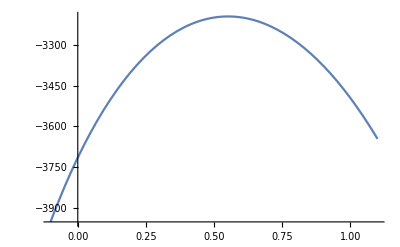

```mathematica
Plot[LogLikelihood[BrodyDistribution,ls[[10]]],{w,-0.1,1.1}]
```

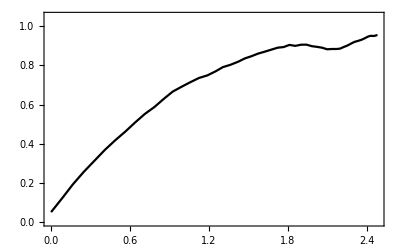

```mathematica
pbrodytest=ListPlot[blist,Joined->True,PlotRange->{0,1.05},PlotStyle->Black,Frame->True,LabelStyle->Large]
```

```mathematica
NewBrodyBC=Table[BinCounts[ls[[ic]],{bins}],{ic,1,50}];
NormalizedBrodyBC=Table[Table[NewBrodyBC[[ic,i]]/Total[NewBrodyBC[[ic]]]/(bins[[i+1]]-bins[[i]]),{i,1,Length[bins]-1}],{ic,1,50}];
RawBrodyHistogram=Table[Table[{bins[[i]],NewBrodyBC[[ic,i]]},{i,1,Length[bins]-1}],{ic,1,50}];
RawFitBrodyHistogram=Table[Table[{bfit[[i]],NewBrodyBC[[ic,i]]},{i,1,Length[bins]-1}],{ic,1,50}];
```

```mathematica
NewBrodyPDist=Table[Table[{bfit[[i]],NormalizedBrodyBC[[ic,i]]},{i,1,Length[bfit]}],{ic,1,50}];
```

```mathematica
BrodyFitNLM=Table[NonlinearModelFit[NewBrodyPDist[[ic]],PBrody[z,w],{w},z,PrecisionGoal->0.001,Method->Automatic,ConfidenceLevel->0.9],{ic,1,50}];
```

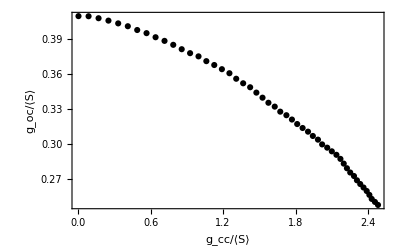

```mathematica
gocdata=Table[{SD[[i,5]],SD[[i,4]]},{i,1,Length[SD]}];
pgocplot=ListPlot[gocdata,PlotStyle->Black,Frame->True,FrameLabel->{"g_cc/⟨S⟩","g_oc/⟨S⟩"},LabelStyle->{12}]
```

```mathematica
brodydata=blist;
brodydataFromNLM=Table[{SD[[ic,5]],w/.BrodyFitNLM[[ic]]["BestFitParameters"]},{ic,1,Length[SD]}];
(*brodyfiterror=Table[BrodyFitNLM[[ic]]["ParameterErrors"][[1]],{ic,1,Length[SD]}];*)
```

```mathematica
brodydatap=Table[{brodydata[[ic,1]],brodydata[[ic,2]]+BrodyError[[ic]]},{ic,1,Length[SD]}];
brodydatam=Table[{brodydata[[ic,1]],brodydata[[ic,2]]-BrodyError[[ic]]},{ic,1,Length[SD]}];
```

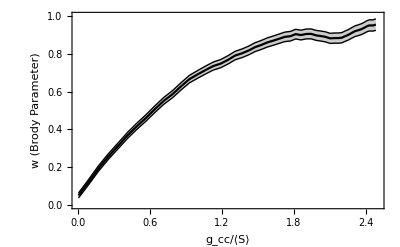

```mathematica
pbrody1=ListPlot[{brodydatam,brodydata,brodydatap},Frame->True,PlotStyle->{{Black,Thin},{Black},{Black,Thin}},Filling->{1->{3}},Joined->True,LabelStyle->Large,FrameLabel->{"g_cc/⟨S⟩","w (Brody Parameter)"},GridLines->None,PlotRange->{{0,2.5},{0,1.0}},Epilog->{Inset[pgocplot,{1.6,.37},{Automatic,Automatic},{1.4,0.7}]}]
```

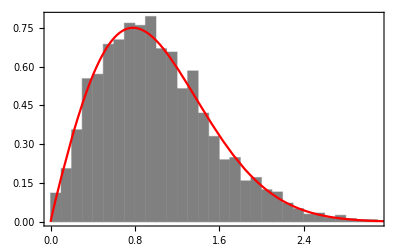

```mathematica
ph1=Histogram[ls[[50]],Automatic,"PDF",ChartStyle->Gray,ChartBaseStyle->EdgeForm[Thin],Frame->True];
pb1=Plot[PBrody[x,blist[[50,2]]],{x,0,5},PlotStyle->Red];
Show[ph1,pb1]
```

```mathematica
0.35698 10^-3 0.24445 10^-2
```

8.72638×10^-7

```mathematica
0.21216 10^-3 0.40287 10^-2
```

8.54729×10^-7

```mathematica
Export["~/Code/Nchannel/Square/CODES/plots/pbrody.pdf",pbrody1]
```

~/Code/Nchannel/Square/CODES/plots/pbrody.pdf

```mathematica
yrange={-0.05,1.15};
```

```mathematica
impad1={{80,10},{95,5}};imagewidth=400;options1={PlotRange->{All,yrange},Frame->True,GridLines->Automatic,LabelStyle->Large,ImageSize->{imagewidth,300},ImagePadding->impad1,FrameTicksStyle->{None,Automatic},AspectRatio->Full};
```

```mathematica
NormalizedBrodyDist=Table[Table[{bins[[i]],NormalizedBrodyBC[[ic,i]]},{i,1,Length[bins]-1}],{ic,1,50}];
```

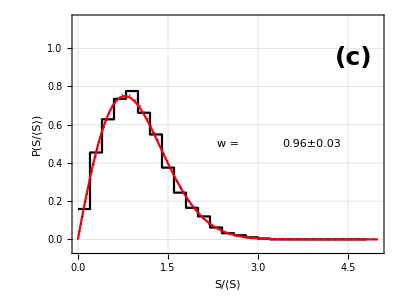

```mathematica
ic=50;
pwigner=Show[ListPlot[NormalizedBrodyDist[[ic]],FrameLabel->{"S/⟨S⟩","P(S/⟨S⟩)"},options1,InterpolationOrder->0,Joined->True,PlotStyle->Black],Plot[{PBrody[x,brodydata[[ic,2]]],PBrody[x,1]},{x,0,5},PlotStyle->{{Red},{Blue,Dotted}}],options1,Epilog->{Text[Style["w = ",Large],{2.5,0.5}],Text[Style[NumberForm[brodydata[[ic,2]],{2,2}]±NumberForm[BrodyError[[ic]],{3,2}],Large],{3.9,0.5}],Text[Style["(c)",25,Bold],{4.6,0.95}]},PlotRangeClipping->False]
```

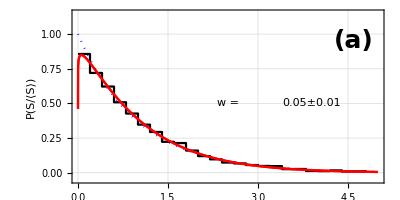

```mathematica
ic=1;
impad2={{80,10},{7,2}};
options={PlotRange->{All,yrange},Frame->True,GridLines->Automatic,LabelStyle->Large,ImageSize->{imagewidth,200},ImagePadding->impad2,FrameTicksStyle->{{Automatic,Automatic},{Directive[FontOpacity->0,FontSize->0],Automatic}},AspectRatio->Full};
ppoisson=Show[ListPlot[NormalizedBrodyDist[[ic]],options1,InterpolationOrder->0,FrameLabel->{None,"P(S/⟨S⟩)"},Joined->True,PlotStyle->Black],Plot[{PBrody[x,brodydata[[ic,2]]],PBrody[x,0.00000001]},{x,0,5},PlotStyle->{{Red},{Blue,Dotted}}],Plot[PBrody[x,brodydata[[ic,2]]],{x,0,5},PlotStyle->Red],options,Epilog->{Text[Style["w = ",Large],{2.5,0.5}],Text[Style[NumberForm[brodydata[[ic,2]],{3,2}]±NumberForm[BrodyError[[ic]],{3,2}],Large],{3.9,0.5}],Text[Style["(a)",25,Bold],{4.6,.95}]},PlotRangeClipping->False]
```

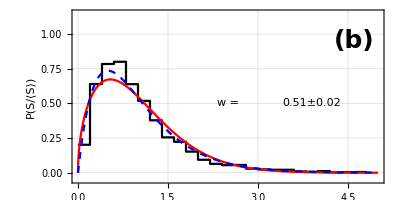

```mathematica
ic=9;
pmiddle=Show[{ListPlot[NormalizedBrodyDist[[ic]],options,InterpolationOrder->0,Joined->True,PlotStyle->Black,FrameLabel->{None,"P(S/⟨S⟩)"}],Plot[PBrody[x,brodydata[[ic,2]]],{x,0,5},PlotStyle->Red],Plot[4 s Exp[-2 s],{s,0,5},PlotStyle->{Blue,Dashed}]},options,Epilog->{Text[Style["w = ",Large],{2.5,0.5}],Text[Style[NumberForm[brodydata[[ic,2]],{3,2}]±NumberForm[BrodyError[[ic]],{3,2}],Large],{3.9,0.5}],(*Text[Style["SE_SP = ",Large],{3.0,0.3}],Text[Style[NumberForm[FitError[SemiPoisson,pfit,Null],{2,2}],Large],{3.9,0.3}]*),
Text[Style["(b)",25,Bold],{4.6,.95}]},PlotRangeClipping->False]
```

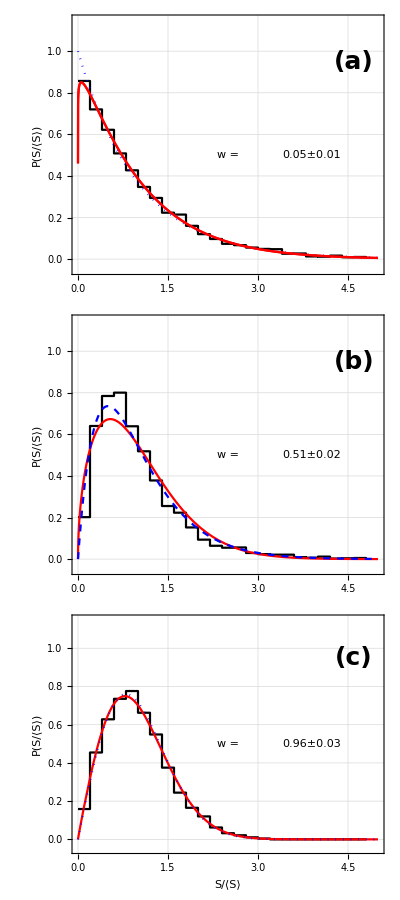

```mathematica
pstats=Grid[{{ppoisson},{pmiddle},{pwigner}},Spacings->0]
```

```mathematica
Export["~/Code/Nchannel/Square/CODES/plots/pstats.pdf",pstats]
```

~/Code/Nchannel/Square/CODES/plots/pstats.pdf

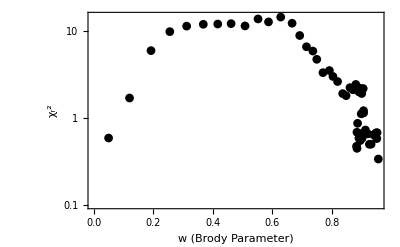

```mathematica
pbrodychisqr=ListLogPlot[Table[
{w/.r1[[ic]],RedChiSqr[PBrody,RawFitBrodyHistogram[[ic]],w/.r1[[ic]],1]},{ic,1,50}],PlotRange->{0.1,15},FrameTicks->{{All,None},{All,None}},Frame->True,PlotMarkers->{"●",8.96},PlotStyle->Black(*,Joined->True*),LabelStyle->Large,FrameLabel->{"w (Brody Parameter)","χ_r^2"},GridLines->None,PlotRange->All]
(*pbrodychisqr=ListPlot[Table[
{SD[[ic,5]],Total[(nlmbrody[[ic]]["FitResiduals"])^2]},{ic,1,50}],Frame->True,PlotStyle->Black,Joined->True,LabelStyle->Large,FrameLabel->{"g_cc/⟨D⟩","χ^2"},GridLines->None,PlotRange->All]*)
```

```mathematica
RedChiSqr[SemiPoisson,RawFitBrodyHistogram[[9]],Null,0]
```

4.02358

```mathematica
Graphics`PlotMarkers[]
```

{{●,8.96},{■,8.96},{◆,10.88},{▲,10.24},{▼,10.24},{○,10.24},{□,10.24},{◇,10.24},{△,11.136},{▽,11.136}}

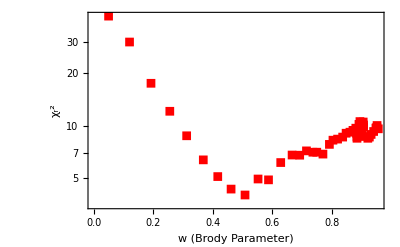

```mathematica
pspchisqr=ListLogPlot[Table[
{w/.r1[[ic]],RedChiSqr[SemiPoisson,RawFitBrodyHistogram[[ic]],Null,0]},{ic,1,50}],Frame->True,PlotMarkers->{"■",8.96},PlotStyle->{Red,Dashed},(*Joined->True,*)LabelStyle->Large,FrameLabel->{"w (Brody Parameter)","χ_r^2"},GridLines->None,FrameTicks->{{All,None},{All,None}}]
```

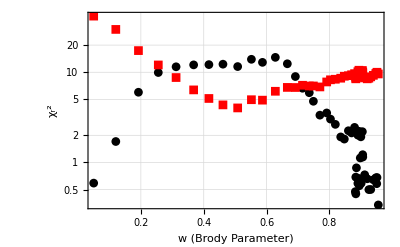

```mathematica
pchisqr=Show[{pbrodychisqr,pspchisqr},PlotRange->All,GridLines->Automatic]
```

```mathematica
Export["~/Code/Nchannel/Square/CODES/plots/ChiSqrPlot.pdf",pchisqr]
```

~/Code/Nchannel/Square/CODES/plots/ChiSqrPlot.pdf

```mathematica
LLratio=Table[{w/.r1[[ic]],-2(LogLikelihood[BrodyDistribution/.r1[[ic]],ls[[ic]]]-LogLikelihood[SemiPoissonDistribution,ls[[ic]]])},{ic,1,50}]
```

{{0.0499654,-1136.03},{0.12031,-578.511},{0.192342,-201.872},{0.255456,3.85518},{0.312029,112.623},{0.367889,174.804},{0.416437,181.638},{0.461146,171.296},{0.507934,149.677},{0.551645,121.425},{0.58677,71.3002},{0.627763,35.0141},{0.665902,-0.490994},{0.69149,-35.793},{0.714167,-66.2329},{0.735682,-95.7127},{0.748762,-120.735},{0.769472,-135.711},{0.791131,-157.549},{0.803094,-176.066},{0.818632,-190.304},{0.835699,-208.989},{0.847166,-227.148},{0.860136,-241.344},{0.870283,-249.324},{0.879756,-259.673},{0.890347,-268.361},{0.89366,-270.558},{0.90458,-280.011},{0.899762,-277.869},{0.905678,-277.229},{0.90589,-273.604},{0.897901,-266.109},{0.894926,-259.016},{0.890297,-254.035},{0.88223,-248.899},{0.883776,-242.121},{0.883657,-235.956},{0.885711,-236.939},{0.893603,-239.183},{0.900819,-239.191},{0.911948,-243.872},{0.920108,-246.253},{0.925237,-250.279},{0.931174,-252.207},{0.939581,-258.522},{0.947278,-264.839},{0.951065,-268.252},{0.950262,-267.33},{0.955276,-268.623}}

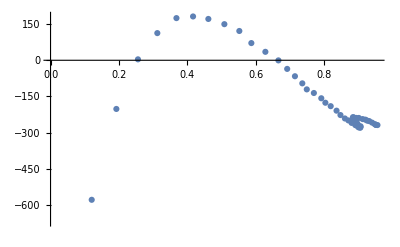

```mathematica
ListPlot[Table[{w/.r1[[ic]],-2Log[Likelihood[BrodyDistribution/.r1[[ic]],ls[[ic]]]/Likelihood[SemiPoissonDistribution,ls[[ic]]]]},{ic,1,50}]]
```

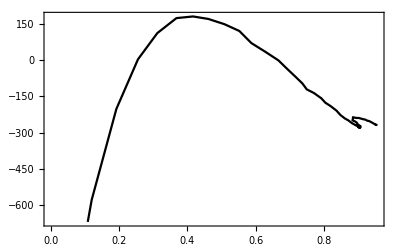

```mathematica
ListPlot[LLratio,Joined->True,PlotStyle->Black,Frame->True,LabelStyle->Large]
```

```mathematica
Length[ARD]
```

163128

### Number variance of resonances

```mathematica
ic=50;iens=2;
DataKeep=Select[ARD,(#1[[3]]==ic && #1[[2]]==iens)&];
nw=Length[DataKeep]
```

24

```mathematica
rpos=Table[DataKeep[[i,5]],{i,1,nw}]
```

{0.0025048,0.0044937,0.013442,0.018354,0.01974,0.022861,0.027451,0.028615,0.031919,0.038395,0.040348,0.049826,0.053422,0.057946,0.060167,0.065107,0.070435,0.074552,0.078588,0.082017,0.08484,0.089559,0.092336,0.094748}

```mathematica
tab1=Table[{DataKeep[[i,5]],i-1},{i,1,nw}];
f1=Interpolation[tab1,InterpolationOrder->0]
```

InterpolatingFunction[{{0.0025048, 0.094748}}, <>]

```mathematica
rpos
```

{0.0025048,0.0044937,0.013442,0.018354,0.01974,0.022861,0.027451,0.028615,0.031919,0.038395,0.040348,0.049826,0.053422,0.057946,0.060167,0.065107,0.070435,0.074552,0.078588,0.082017,0.08484,0.089559,0.092336,0.094748}

0.1

InterpolatingFunction::dmval: Input value {2.04286×10^-6} lies outside the range of data in the interpolating function. Extrapolation will be used.

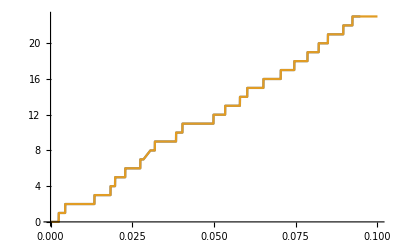

```mathematica
Emin=0.0;Emax=0.1
Plot[{(i=FirstPosition[rpos,u_/;u>EE,0][[1]];i-1),f1[EE]},{EE,Emin,Emax}]
```

InterpolatingFunction::dmval: Input value {1.01111×10^-6} lies outside the range of data in the interpolating function. Extrapolation will be used.

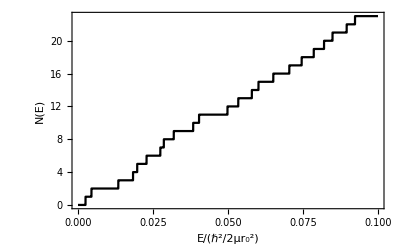

```mathematica
Plot[f1[EE],{EE,Emin,Emax},Frame->True,LabelStyle->Large,PlotStyle->Black,FrameLabel->{"E/(ℏ^2/2μr_0^2)","N(E)"},PlotPoints->100]
```

```mathematica
DataKeep=Select[ARD,(#1[[3]]==ic && #1[[2]]==iens)&];
```

```mathematica
NumEns=100;
```

```mathematica
NETable=Table[
DataKeep=Select[ARD,(#1[[3]]==ic && #1[[2]]==iens)&];nw=Length[DataKeep];Table[{DataKeep[[i,5]],i-1},{i,1,nw}],
{ic,1,Length[SD]},{iens,1,NumEns}];
```

```mathematica
Export["~/Code/Nchannel/Square/CODES/plots/NETable.dat",NETable,"List"]
```

~/Code/Nchannel/Square/CODES/plots/NETable.dat

```mathematica
NETablei=Import["~/Code/Nchannel/Square/CODES/plots/NETable.dat","List"];
```

```mathematica
fall=Table[
Interpolation[NETable[[ic,iens]],InterpolationOrder->0],{ic,1,Length[SD]},{iens,1,NumEns}];
```

InterpolatingFunction::dmval: Input value {1.01111×10^-6} lies outside the range of data in the interpolating function. Extrapolation will be used.

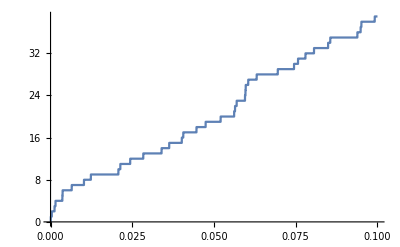

```mathematica
Plot[fall[[1,1]][Energy],{Energy,Emin,Emax},PlotPoints->100]
```

```mathematica
0.1/0.004/4
```

6.25

```mathematica
NERange[ΔE_,E0_,ic_,iens_]:=fall[[ic,iens]][E0+ΔE]-fall[[ic,iens]][E0]
```

```mathematica
Plot[NERange[ΔE,0.,1,1],{ΔE,Emin,Emax},PlotPoints->100]
```

InterpolatingFunction::dmval: Input value {1.01111×10^-6} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.} lies outside the range of data in the interpolating function. Extrapolation will be used.

-Graphics-

```mathematica
NumEns=100;
Emin=0.0;Emax=0.1;NumWindows=Table[(Emax-Emin)/SD[[ic,3]]/4,{ic,1,Length[SD]}]
```

{10.227,10.2249,10.1825,10.1313,10.0725,10.012,9.93167,9.86466,9.77746,9.70007,9.61612,9.52272,9.43824,9.37031,9.26818,9.18577,9.09719,9.01096,8.89363,8.79662,8.71202,8.59786,8.49041,8.38223,8.29958,8.19216,8.11688,8.02439,7.92845,7.84461,7.76639,7.6746,7.59624,7.4949,7.42567,7.34754,7.27336,7.18639,7.08577,6.98734,6.89636,6.82128,6.73056,6.65124,6.5767,6.50229,6.41947,6.33376,6.26975,6.20548}

```mathematica
ic1=1;ic2=9;ic3=50;
```

InterpolatingFunction::dmval: Input value {0.} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

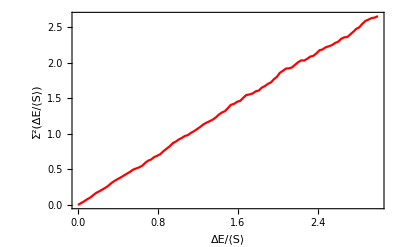

```mathematica
ΔEmax=(Emax-Emin)/13;
Erange=Table[EE,{EE,Emin,Emax,ΔEmax}];
nerange=Length[Erange]-1;
psigma2c1=Plot[Evaluate[Table[(
Sum[(NERange[DE,Erange[[ie]],ic,iens])^2,{iens,1,NumEns},{ie,1,nerange}]/(NumEns*nerange)
-(Sum[NERange[DE,Erange[[ie]],ic,iens],{iens,1,NumEns},{ie,1,nerange}]/(NumEns*nerange))^2)/.DE->DEOverD SD[[ic,3]],
{ic,{ic1}}]],
{DEOverD,0,3},PlotPoints->50,MaxRecursion->1,
PlotStyle->{{Red},{Green},{Blue}},
Frame->True,
LabelStyle->Large,
FrameLabel->{"ΔE/⟨S⟩","Σ^2(ΔE/⟨S⟩)"}]
```

InterpolatingFunction::dmval: Input value {0.} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

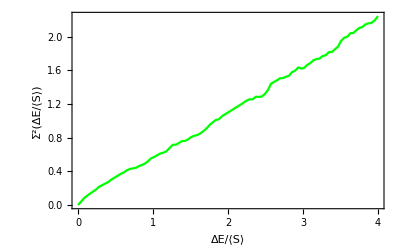

```mathematica
ΔEmax=(Emax-Emin)/7.;
Erange=Table[EE,{EE,Emin,Emax,ΔEmax}];
nerange=Length[Erange]-1;
psigma2cmid=Plot[Evaluate[Table[(
Sum[(NERange[DE,Erange[[ie]],ic,iens])^2,{iens,1,NumEns},{ie,1,nerange}]/(NumEns*nerange)
-(Sum[NERange[DE,Erange[[ie]],ic,iens],{iens,1,NumEns},{ie,1,nerange}]/(NumEns*nerange))^2)/.DE->DEOverD SD[[ic,3]],
{ic,{ic2}}]],
{DEOverD,0,4},PlotPoints->50,MaxRecursion->1,
PlotStyle->{{Green},{Green},{Blue}},
Frame->True,
LabelStyle->Large,
FrameLabel->{"ΔE/⟨S⟩","Σ^2(ΔE/⟨S⟩)"}]
```

InterpolatingFunction::dmval: Input value {0.} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

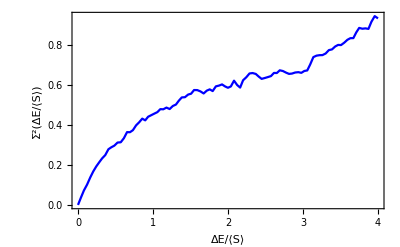

```mathematica
ΔEmax=(Emax-Emin)/6.;
Erange=Table[EE,{EE,Emin,Emax,ΔEmax}];
nerange=Length[Erange]-1;
psigma2cwigner=Plot[Evaluate[Table[(
Sum[(NERange[DE,Erange[[ie]],ic,iens])^2,{iens,1,NumEns},{ie,1,nerange}]/(NumEns*nerange)
-(Sum[NERange[DE,Erange[[ie]],ic,iens],{iens,1,NumEns},{ie,1,nerange}]/(NumEns*nerange))^2)/.DE->DEOverD SD[[ic,3]],
{ic,{ic3}}]],
{DEOverD,0,4},PlotPoints->50,MaxRecursion->1,
PlotStyle->{{Blue},{Green},{Blue}},
Frame->True,
LabelStyle->Large,
FrameLabel->{"ΔE/⟨S⟩","Σ^2(ΔE/⟨S⟩)"}]
```

```mathematica
pSP=Plot[L/2+(1-Exp[-4 L])/8,{L,0,4},PlotStyle->{Black,Dotted}];
Sig2Formula[β_,r_]:=2/(β π^2)(Log[β π r]+EulerGamma+1-Cos[β π r]-CosIntegral[β π r]) + r(1-2/π SinIntegral[β π r]);
Sig2GOE[r_]:=2 Sig2Formula[2,r]+(SinIntegral[π r]/π)^2-1/π SinIntegral[π r];
psigendcases=Plot[{Sig2Formula[0.001,r],Sig2GOE[r]},{r,0,4},PlotStyle->{{Black,Dashed},{Black,Dashed}}];
```

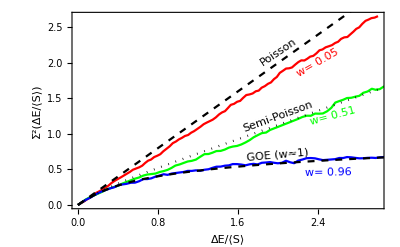

```mathematica
psig2=Show[psigma2c1,psigma2cmid,psigma2cwigner,pSP,psigendcases,
Epilog->{
Text[Style[Rotate["Poisson",34 Degree],Medium],{2.0,2.15}],
Text[Style[Rotate["Semi-Poisson",20 Degree],Medium],{2.0,1.25}],
Text[Style[Rotate["GOE (w≈1)",5 Degree],Medium],{2.0,0.7}],
Text[Style[Rotate[StringJoin["w= ",ToString[NumberForm[brodydata[[ic1,2]],{2,2}]]],30 Degree],{Medium,Red}],{2.4,2.0}],
Text[Style[Rotate[StringJoin["w= ",ToString[NumberForm[brodydata[[ic2,2]],{2,2}]]],15 Degree],{Medium,Green}],{2.55,1.25}],
Text[Style[Rotate[StringJoin["w= ",ToString[NumberForm[brodydata[[ic3,2]],{2,2}]]],1 Degree],{Medium,Blue}],{2.5,.45}]}]
```

```mathematica
TraditionalForm[Sig2GOE[ϵ]]
```

2 ((-2 π ϵ+log(2 π ϵ)-cos(2 π ϵ)+ℽ+1)/π^2+ϵ (1-(2 2 π ϵ)/π))+(π ϵ)^2/π^2-(π ϵ)/π

```mathematica
Export["~/Code/Nchannel/Square/CODES/plots/psigma2.pdf",psig2]
```

~/Code/Nchannel/Square/CODES/plots/psigma2.pdf

### What to expect for semi-poisson?

If we sample the semi-poisson distribution, what Brody parameter do we expect, and with what standard error?

```mathematica
cumsp[s_]:=Integrate[4s Exp[-2s],{s,0,s}]
```

```mathematica
cumsp[s]
```

ⅇ^(-2 s) (-1+ⅇ^(2 s)-2 s)

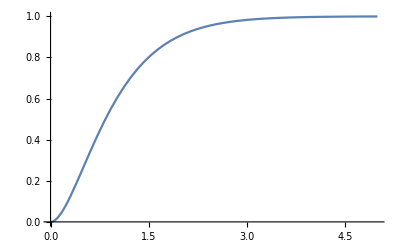

```mathematica
Plot[ⅇ^(-2 s) (-1+ⅇ^(2 s)-2 s),{s,0,5}]
```

```mathematica
spacing[u_]:=s/.FindRoot[u==ⅇ^(-2 s) (-1+ⅇ^(2 s)-2 s),{s,0.5},AccuracyGoal->5][[1]]
```

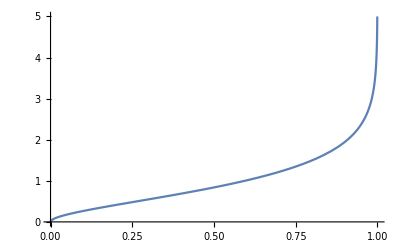

```mathematica
Plot[spacing[u],{u,0,1},PlotRange->{0,5}]
```

```mathematica
spacing[.9999]
```

5.87819

```mathematica
SeedRandom[1];SPSample[n_]:=Module[{u,z},u=RandomReal[{0,0.9999999},n];Map[spacing,u]]
samp=SPSample[10000];
spw=FindDistributionParameters[samp,BrodyDistribution]
√(-1/D[LogLikelihood[BrodyDistribution,samp],{w,2}])/.spw
```

{w→0.494678}

0.0110972

```mathematica
SeedRandom[2];SPSample[n_]:=Module[{u,z},u=RandomReal[{0,0.9999999},n];Map[spacing,u]]
samp=SPSample[10000];
spw=FindDistributionParameters[samp,BrodyDistribution]
√(-1/D[LogLikelihood[BrodyDistribution,samp],{w,2}])/.spw
```

{w→0.495638}

0.0111125

```mathematica
Clear[a,x,P,dx];
Simplify[LogLikelihood[ProbabilityDistribution[P[a,x] dx,{x,0,∞},Assumptions->{a>0}],{x1,x2,x3,x4,x5}],{x1>0,x2>0,x3>0,x4>0,x5>0,dx>0}]
```

5 Log[dx]+Log[P[a,x1]]+Log[P[a,x2]]+Log[P[a,x3]]+Log[P[a,x4]]+Log[P[a,x5]]

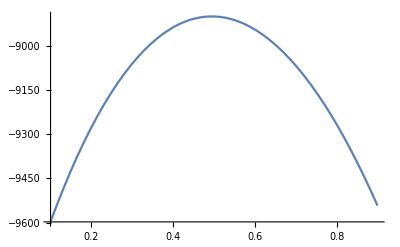

```mathematica
Plot[LogLikelihood[BrodyDistribution,samp],{w,0.1,0.9}]
```

```mathematica
√(-1/D[LogLikelihood[BrodyDistribution,samp],{w,2}])/.spw
```

0.0110972

```mathematica
spbc=BinCounts[samp,{bins}]
```

{621,1224,1462,1398,1178,1017,821,583,440,347,246,180,140,107,66,39,37,33,27,9,7,7,3,3,3}

```mathematica
sphist=Table[{(bins[[i]]+bins[[i+1]])/2,spbc[[i]]},{i,1,Length[bins]-1}]
```

{{0.1,621},{0.3,1224},{0.5,1462},{0.7,1398},{0.9,1178},{1.1,1017},{1.3,821},{1.5,583},{1.7,440},{1.9,347},{2.1,246},{2.3,180},{2.5,140},{2.7,107},{2.9,66},{3.1,39},{3.3,37},{3.5,33},{3.7,27},{3.9,9},{4.1,7},{4.3,7},{4.5,3},{4.7,3},{4.9,3}}

```mathematica
RedChiSqr[SemiPoisson,sphist,Null,0]
```

1.10886

```mathematica
RedChiSqr[PBrody,sphist,0.5,1]
```

6.1015

```mathematica
ChiSqr[func_,hist_,p_]:=Module[{tab1,nbin,dbin,Ntot},
dbin=hist[[2,1]]-hist[[1,1]];
Ntot=Total[hist[[All,2]]];
tab1=Table[(hist[[i,2]]-Ntot  dbin func[hist[[i,1]],p])^2/(Ntot dbin  func[hist[[i,1]],p]),{i,1,Length[hist]}];
Print[p];
If[p== Null,
tab1=Table[(hist[[i,2]]-Ntot  dbin func[hist[[i,1]]])^2/(Ntot dbin  func[hist[[i,1]]]),{i,1,Length[hist]}]
];
nbin=Length[hist];
Total[tab1]
]
```

```mathematica
Var[func_,P_]:=Module[{tab1,nbin,dbin,Ntot},
dbin=P[[2,1]]-P[[1,1]];
Ntot=Total[P[[All,2]]];
tab1=Table[0,{i,1,Length[P]}];
tab1=Table[(P[[i,2]]-func[P[[i,1]]])^2,{i,1,Length[P]}];

nbin=Length[P];
1/(nbin-1)Total[tab1]
]
```

```mathematica
bc=BinCounts[samp,{Bins}];
bcnorm=bc/NP/dx;
bnorm=Table[{(Bins[[i]]),bcnorm[[i]]},{i,1,Length[Bins]-1}];
bcfit=Table[{(Bins[[i]]+Bins[[i+1]])/2,bc[[i]]},{i,1,Length[Bins]-1}];
bfit=Table[{(Bins[[i]]+Bins[[i+1]])/2,bcnorm[[i]]},{i,1,Length[Bins]-1}];
```

```mathematica
ChiSqr[SemiPoisson,bcfit,Null]
```

Null

30.5108

```mathematica
ChiSqr[PBrody,bcfit,0.53]
```

0.53

150.651

```mathematica
Var[SemiPoisson,bfit]
```

Var[SemiPoisson,{{0.1,0.298},{0.3,0.661},{0.5,0.707},{0.7,0.705},{0.9,0.595},{1.1,0.506},{1.3,0.378},{1.5,0.2965},{1.7,0.2395},{1.9,0.159},{2.1,0.122},{2.3,0.0985},{2.5,0.07},{2.7,0.0435},{2.9,0.0345},{3.1,0.0315},{3.3,0.0165},{3.5,0.0155},{3.7,0.008},{3.9,0.0045},{4.1,0.006},{4.3,0.0005},{4.5,0.001},{4.7,0.001},{4.9,0.}}]

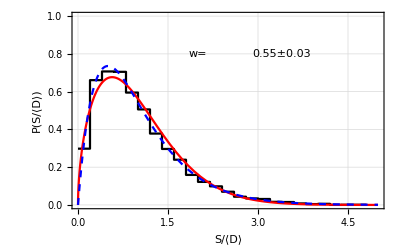

```mathematica
ph=ListPlot[bnorm,InterpolationOrder->0,Joined->True,PlotStyle->Black];
psp=Plot[4s Exp[-2s],{s,0,5},PlotStyle->{Blue,Dashed}];
nlm=NonlinearModelFit[bfit,{PBrody[z,w]},{{w,w0}},z,Method->"LevenbergMarquardt",ConfidenceLevel->0.9999];
pb=Plot[PBrody[z,w/.nlm["BestFitParameters"]],{z,0,5},PlotStyle->{Red}];
Show[{ph,pb,psp},PlotRange->{0,1},Frame->True,GridLines->Automatic,FrameLabel->{"S/⟨D⟩","P(S/⟨D⟩)"},LabelStyle->Large,Epilog->{
(*Text[Style["SE_SP= ",Large],{3.3,0.3}],*)
Text[Style["w=",Large],{2,0.8}],
(*Text[Style[NumberForm[FitError[SemiPoisson,bfit,Null],{2,2}],Large],{4.2,0.3}],*)Text[Style[NumberForm[w/.nlm["BestFitParameters"],{2,2}]±NumberForm[FitError[PBrody,bfit,w/.nlm["BestFitParameters"]],{2,2}],Large],{3.4,0.8}]}]
```

### Potential Alternatives to the Brody distribution

Are there other functions that extrapolate between the Poisson and Wigner limits?  The SP distribution appears to have the right idea, but doesn’t produce a χ^2≈1, so can we imagine another family of functions that achieves the desired goal but with less repulsion at intermediate values of w?

```mathematica
PBrody[s,w]
```

ⅇ^(-(s Gamma[(2+w)/(1+w)])^(1+w)) s^w (1+w) Gamma[(2+w)/(1+w)]^(1+w)

```mathematica
PBrody[s,0]
```

ⅇ^-s

```mathematica
PBrody[s,1]
```

1/2 ⅇ^(-(π s^2)/4) π s

```mathematica
SemiPoisson[s]
```

4 ⅇ^(-2 s) s

```mathematica
(Gamma[2+w]/Gamma[1+w])^(1+w)/.w->1
```

4

```mathematica
ⅇ^(-( Gamma[(2+w)/(1+w)])^(1+w)) /.w->1
```

ⅇ^(-π/4)

```mathematica
1/Integrate[ⅇ^(-(1+(π/4-1)w)s^(1+w)) s^w ,{s,0,∞},Assumptions->{w>0,w<1}]
```

1/4 (1+w) (4+(-4+π) w)

```mathematica
Integrate[((1+w) (4+(-4+π) w))/4 ⅇ^(-(1+(π/4-1)w)s^(1+w)) s^w,{s,0,∞},Assumptions->{w>0,w<1}]
```

1

```mathematica
PAlternative[s_,w_]:=((1+w) (4+(-4+π) w))/4 ⅇ^(-(1+(π/4-1)w)s^(1+w)) s^w
```

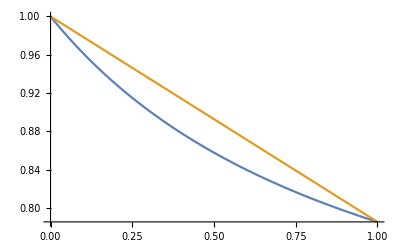

```mathematica
Plot[{(Gamma[(2+w)/(1+w)])^(1+w),1+(π/4-1)w},{w,0,1}]
```

```mathematica
AlternativeLSFit=Table[NonlinearModelFit[NewBrodyPDist[[ic]],PAlternative[z,w],{w},z,PrecisionGoal->0.001,Method->Automatic,ConfidenceLevel->0.9],{ic,1,50}];
```

```mathematica
AlternativeLSFit[[9]]["ParameterErrors"]
```

{0.0501891}

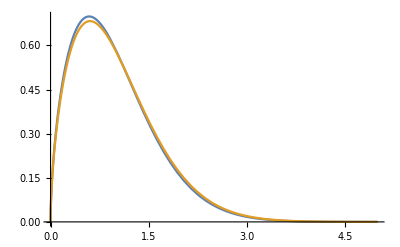

```mathematica
Plot[{PAlternative[s,.6],PBrody[s,.6]},{s,0,5}]
```

```mathematica
PBrody[s,1]
```

1/2 ⅇ^(-(π s^2)/4) π s